```mathematica
FullSimplify[y/.Solve[PDF[MultinormalDistribution[{0,0},{{1,0.45},{0.45,1}}],{x,y}]/Integrate[PDF[MultinormalDistribution[{0,0},{{1,0.45},{0.45,1}}],{x,y}],{y,-Infinity,Infinity}]==0.5,y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(0.-0.423892 ⅈ)+0.45 x,(0.+0.423892 ⅈ)+0.45 x}

```mathematica
FullSimplify[x/.Solve[PDF[MultinormalDistribution[{0,0},{{1,0.45},{0.45,1}}],{x,y}]/Integrate[PDF[MultinormalDistribution[{0,0},{{1,0.45},{0.45,1}}],{x,y}],{x,-Infinity,Infinity}]==0.5,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(0.-0.423892 ⅈ)+0.45 y,(0.+0.423892 ⅈ)+0.45 y}

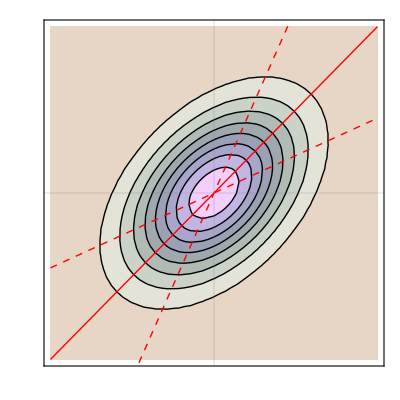

```mathematica
p1=ContourPlot[PDF[MultinormalDistribution[{0,0},{{1,0.45},{0.45,1}}],{x,y}],{x,-3,3},{y,-3,3},ColorFunction->"PearlColors",PlotTheme->"Scientific",FrameTicks->None];
p2=Plot[0.45x,{x,-3,3},PlotStyle->{Red,Thick,Dashed}];
p3=Plot[x/0.45,{x,-3,3},PlotStyle->{Red,Thick,Dashed}];
p4=Plot[x,{x,-3,3},PlotStyle->{Red,Thick}];
Show[p1,p2,p3,p4]
```